## Figure 3A, 3B (p=2 nutrients)

Evaluate notebook to generate plots for Fig. 3A, B (the oligotroph condition for p=2 nutrients)

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
```

```mathematica
s1List={0.1,0.2,0.3,.35,0.4,.45,0.5};
nameStringList=Table[ToString[s1List[[i]]],{i,Length[s1List]}];
numTests=Length[nameStringList];
```

```mathematica
namePt1="data//2nutrients//statisticalCoexistence_pbc_m20_s1=";
namePt2="_d=1_l=Sqrt[10]_fixedPoints_trajectories_alphas.mx";
```

### get colorscheme data

```mathematica
(*Read in the numerical data*)Get["https://pastebin.com/raw/gN4wGqxe"]
ParulaCM=With[{colorlist=RGBColor@@@parulaColors},Blend[colorlist,#]&];
Cube1CM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
CubeYFCM=With[{colorlist=RGBColor@@@cubeYFColors},Blend[colorlist,#]&];
LinearLCM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
JetCM=With[{colorlist=RGBColor@@@jetColors},Blend[colorlist,#]&];
```

### import data

```mathematica
fixedPoints={};
s={};
alphas={};
```

```mathematica
For[i=1,i≤numTests,i++,
name=namePt1<>nameStringList[[i]]<>namePt2;
thisData=Import[name];
fixedPoints=Join[fixedPoints,{thisData[[1]]}];
s=Join[s,{thisData[[2]]}];
alphas=Join[alphas,{thisData[[3]]}];

];
m=Length[alphas[[1,1]]];
numTrials=Length[alphas[[1]]];
```

```mathematica
e=1;
supply=1;
sScaled=(e/supply)*s;
```

### calculate M=effective number of species

```mathematica
shannonEntropy[n_]:=
Module[{modN,entropyTable,entropyTable2,entropy},
modN=n/.{x_/;x<0->0};
entropyTable=Table[-modN[[i]]*Log[modN[[i]]],{i,Length[modN]}]//Quiet;
entropyTable2=entropyTable/.{Indeterminate->0};
entropy=entropyTable2//Total
]
```

```mathematica
total=Sqrt[10];
```

```mathematica
entropy=ConstantArray[0,numTests];
effectiveSpecies=ConstantArray[0,numTests];
entropyHist=ConstantArray[0,numTests];
```

```mathematica
For[i=1,i<=numTests,i++,
proportionalFP=Table[fixedPoints[[i,j]]/total,{j,numTrials}];

entropy[[i]]=Table[shannonEntropy[proportionalFP[[k]]],{k,numTrials}];
effectiveSpecies[[i]]=Table[E^entropy[[i,k]],{k,numTrials}];

]
```

### strategies in diverse communities (3B)

```mathematica
trial=5;
```

```mathematica
cutoff=Quantile[effectiveSpecies[[trial]],.9];
```

```mathematica
diversePositions=Position[effectiveSpecies[[trial]],x_/;x>cutoff];
```

```mathematica
diverseAlphas=Flatten[Table[alphas[[trial,diversePositions[[i]]]],{i,Length[diversePositions]}],1];
```

```mathematica
p=Graphics[{EdgeForm[{Gray//Darker,Thin}],FaceForm[ColorData[97,2]],Disk[]}];
```

```mathematica
diverseAlphasPlotting=diverseAlphas//Flatten;
```

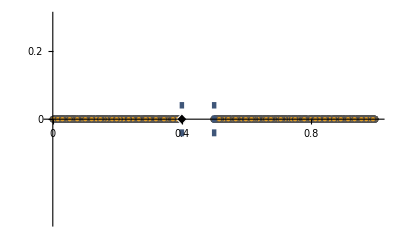

```mathematica
Show[ListPlot[Table[{diverseAlphasPlotting[[i]],0},{i,Length[diverseAlphasPlotting]}],Axes->{True,False},AxesStyle->Thick,PlotMarkers->{p,.03},Ticks->{{#,Framed[#,FrameMargins->1,FrameStyle->None]}&/@{0,.2,.4,.6,.8,1}},TicksStyle->Directive[Black,12],PlotRange->{{-0.007,1.006},{-0.3,.3}}],Graphics[{Directive[Darker[ColorData[97,1]],Thickness->.008,Dashed,CapForm[None]],Line[{{.5,-.05},{.5,.05}}],Line[{{.4,-.05},{.4,.05}}]}],Graphics[{EdgeForm[{White}],Polygon[{{.4-.016,0},{.4,.016},{.4+.016,0},{.4,-.016}}]}],Method->{"AxesInFront"->False}]
```

```mathematica
Export["fig3B_2nutrients_diverseStrategies.svg",%];
```

### Diversity distributions (3A)

```mathematica
(*example with no oligotrophs, Subscript[s, 1]=0.2*)
pt2Data=Import["data//2nutrients//statisticalCoexistence_pbc_m20_s1=0.2_d=1_l=Sqrt[10]_gap_fixedPoints_trajectories_alphas.mx"];
pt2FP=pt2Data[[1]];
pt2S=pt2Data[[2]];
pt2alphas=pt2Data[[3]];
```

```mathematica
proportionalFPpt2=Table[pt2FP[[j]]/total,{j,Length[pt2FP]}];
entropyNoGap=Table[shannonEntropy[proportionalFPpt2[[k]]],{k,numTrials}];
effectiveSpeciesNoGap=Table[E^entropyNoGap[[k]],{k,Length[entropyNoGap]}];
```

```mathematica
includedHist={2,3,4,5,6,7};
plottingSpecies=effectiveSpecies[[includedHist]];
includedS=sScaled[[includedHist]];
colors=ParulaCM/@((includedS-includedS[[1]])/(includedS[[-1]]-includedS[[1]]));
```

```mathematica
threeDCoords=Table[Table[{includedS[[i]],plottingSpecies[[i,j]]},{j,Length[plottingSpecies[[i]]]}],{i,Length[includedHist],1,-1}];
```

```mathematica
effectiveSpeciesNoGapCoords=Table[{.21,effectiveSpeciesNoGap[[i]]},{i,Length[effectiveSpeciesNoGap]}];
```

```mathematica
new3DCoords=Join[threeDCoords,{effectiveSpeciesNoGapCoords}];
```

```mathematica
fullColors=Join[colors//Reverse,{Red}];
```

```mathematica
Histogram3D[new3DCoords,{{.01},{1}},"Probability",Boxed->False,ScalingFunctions->{"Reverse",Identity,Identity},TicksStyle->Black,ChartStyle->fullColors,ViewPoint->{2.8770859632354266,1.3997211835038195,1.1014340509555465},LabelStyle->Directive[Black,14]]
```

-Graphics3D-

```mathematica
Export["fig3A_2nutrients_diversityDistribution.png",%,ImageResolution->600];
```